x^2+3 y^2

{2 x,6 y}

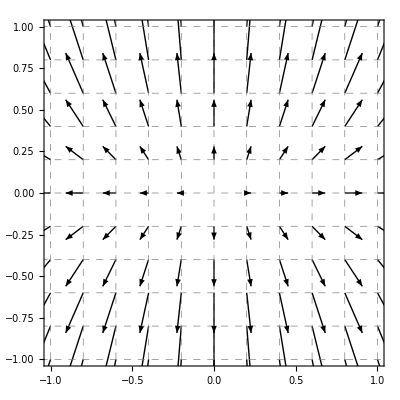

```mathematica
F[x_,y_]=x^2+3y^2
D[F[x,y],{{x,y}}]
vecField=VectorPlot[Evaluate[D[F[x,y],{{x,y}}]],{x,-1,1},{y,-1,1},
PlotRange->{{-1,1},{-1,1}},
GridLines->{{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1},{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1}},
 VectorPoints->11,
VectorStyle-> Black,
VectorScale->{.15,.5},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
F[x_,y_]={-y/(x^2+y^2),x/(x^2+y^2)}
Curl[F[x,y],{x,y}]
```

{-y/(x^2+y^2),x/(x^2+y^2)}

-(2 x^2)/((x^2+y^2)^2)-(2 y^2)/((x^2+y^2)^2)+2/(x^2+y^2)

```mathematica
Integrate[F[x,y][[1]],x]
Integrate[F[x,y][[2]],y]
```

-ArcTan[x/y]

ArcTan[y/x]

```mathematica
Plot3D[{ArcTan[y/x],Pi+ ArcTan[y/x],-Pi+ ArcTan[y/x]},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Simplify[-x^2/((x^2+y^2)^(3/2))-y^2/((x^2+y^2)^(3/2))+2/(√(x^2+y^2))]
```

1/(√(x^2+y^2))

```mathematica
Sqrt[F[x,y].F[x,y]]
```

√(x^2/(x^2+y^2)+y^2/(x^2+y^2))

```mathematica
Simplify[√(x^2/(x^2+y^2)+y^2/(x^2+y^2))]
```

1

```mathematica
Simplify[√(x^2/((x^2+y^2)^2)+y^2/((x^2+y^2)^2))]
```

√(1/(x^2+y^2))

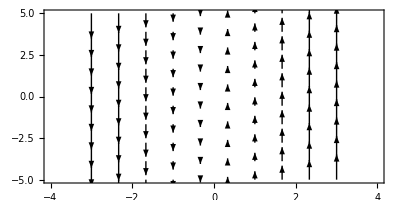

```mathematica
vecField=VectorPlot[{0,x},{x,-3,3},{y,-5,5},
PlotRange->{{-4,4},{-5,5}},AspectRatio->1/2,

 VectorPoints->10,
VectorStyle-> Black,
VectorScale->{.13,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

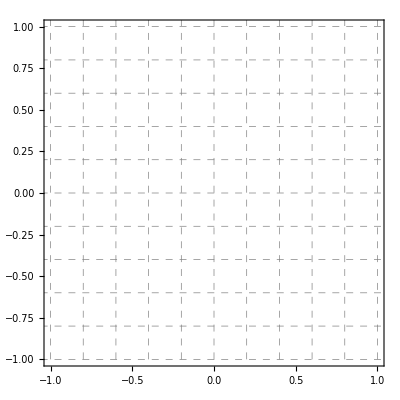

```mathematica
F[x_,y_]={2,3};
vecField=VectorPlot[Evaluate[D[F[x,y],{{x,y}}]],{x,-1,1},{y,-1,1},
PlotRange->{{-1,1},{-1,1}},
GridLines->{{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1},{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1}},
 VectorPoints->11,
VectorStyle-> Black,
VectorScale->{.15,.5},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

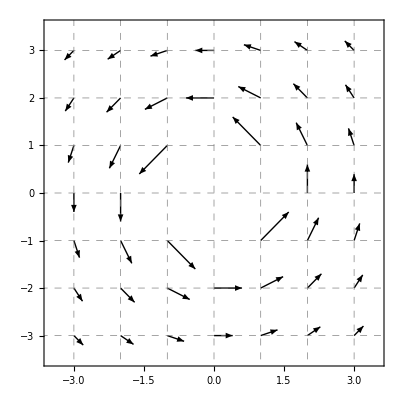

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>1]{-y/(x^2+y^2),x/(x^2+y^2)},{x,-3,3},{y,-3,3},
PlotRange->{{-3.5,3.5},{-3.5,3.5}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/rotFieldNot.png",vecField]
```

~/teaching/mooculus/calculus3/vectorFields/rotFieldNot.png

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/constField.png",vecField]
```

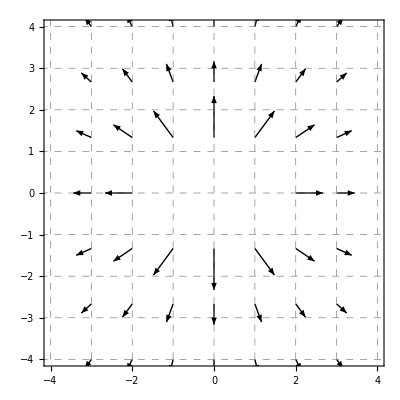

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>1]{x/(x^2+y^2)^(1),y/(x^2+y^2)^(1)},{x,-3,3},{y,-4,4},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/radField1.png",vecField]
```

~/teaching/mooculus/calculus3/vectorFields/radField1.png

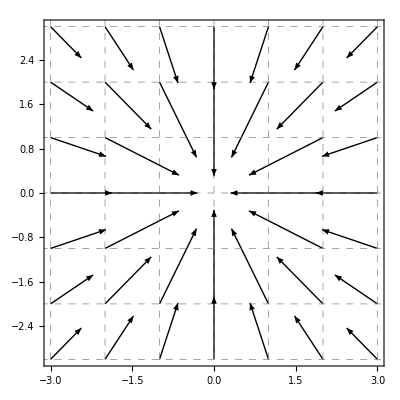

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>3]{-x/(x^2+y^2)^(1),-y/(x^2+y^2)^(1)},{x,-3,3},{y,-3,3},
PlotRange->{{-3,3},{-3,3}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.2,.3},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/radField2.png",vecField]
```

~/teaching/mooculus/calculus3/vectorFields/radField2.png

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/gradAndSurf.png",gradSurf,ImageResolution->300]
```

~/teaching/mooculus/calculus3/vectorFields/gradAndSurf.png

-Graphics3D-

-Graphics3D-

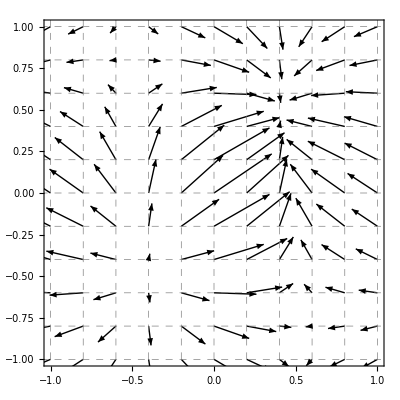

```mathematica
F[x_,y_]=(Sin[3x]+Sin[2y])/(1+x^2+y^2);
samples=Flatten[Table[{x,y,0},{x,-1,1,.2},{y,-1,1,.2}],1];
vecField=VectorPlot3D[Evaluate[Append[D[F[x,y],{{x,y}}],0]],{x,-1,1},{y,-1,1},{z,0,.5},VectorPoints->samples,VectorScale->{.1,.4},VectorStyle->Black];
surface=Plot3D[F[x,y],{x,-1,1},{y,-1,1},PlotStyle->Opacity[.5],Mesh->False,PlotRange->{-2,2},BoxRatios->{1,1,1}]
gradSurf=Show[vecField,surface,PlotRange->{-2,2}]

vecField=VectorPlot[Evaluate[D[F[x,y],{{x,y}}]],{x,-1,1},{y,-1,1},
PlotRange->{{-1,1},{-1,1}},
GridLines->{{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1},{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1}},
 VectorPoints->11,
VectorStyle-> Black,
VectorScale->{.15,.5},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/surf1.png",surface,ImageResolution->300]
```

~/teaching/mooculus/calculus3/vectorFields/surf1.png

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/gradField1.png",vecField]
```

~/teaching/mooculus/calculus3/vectorFields/gradField1.png

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/gradSurf1.png",gradSurf,ImageResolution->300]
```

~/teaching/mooculus/calculus3/vectorFields/gradSurf1.png

1/(√(x^2+y^2))

-Graphics3D-

-Graphics3D-

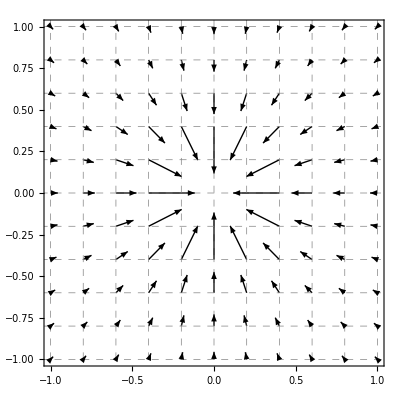

```mathematica
F[x_,y_]=1/Sqrt[x^2+y^2]
samples=Flatten[Table[{x,y,0},{x,-1,1,.2},{y,-1,1,.2}],1];
vecField=VectorPlot3D[Evaluate[Append[D[F[x,y],{{x,y}}],0]],{x,-1,1},{y,-1,1},{z,0,.5},VectorPoints->samples,VectorScale->{.1,.4},VectorStyle->Black];
surface=Plot3D[F[x,y],{x,-1,1},{y,-1,1},PlotStyle->Opacity[.5],Mesh->False,PlotRange->{0,10},BoxRatios->{1,1,1}]
gradSurf=Show[vecField,surface,PlotRange->{0,10}]

vecField=VectorPlot[Boole[x^2+y^2>.1]{-x/Sqrt[(x^2+y^2)]^3,-y/Sqrt[(x^2+y^2)]^3},{x,-1,1},{y,-1,1},
PlotRange->{{-1,1},{-1,1}},
GridLines->{{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1},{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1}},
 VectorPoints->11,
VectorStyle-> Black,
VectorScale->{.1,.9},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/surf2.png",surface,ImageResolution->300]
```

~/teaching/mooculus/calculus3/vectorFields/surf2.png

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/gradField2.png",vecField]
```

~/teaching/mooculus/calculus3/vectorFields/gradField2.png

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/gradSurf2.png",gradSurf,ImageResolution->300]
```

~/teaching/mooculus/calculus3/vectorFields/gradSurf2.png

```mathematica
1
```

1

```mathematica
F[x_,y_]=x^2-y^2
samples=Flatten[Table[{x,y,0},{x,-1,1,.2},{y,-1,1,.2}],1];
vecField=VectorPlot3D[Evaluate[Append[D[F[x,y],{{x,y}}],0]],{x,-1,1},{y,-1,1},{z,0,.5},VectorPoints->samples,VectorScale->{.1,.6},VectorStyle->Black];
surface=Plot3D[F[x,y],{x,-1,1},{y,-1,1},PlotStyle->Opacity[.5],Mesh->False];
gradSurf=Show[vecField,surface]
```

```mathematica
D[
```

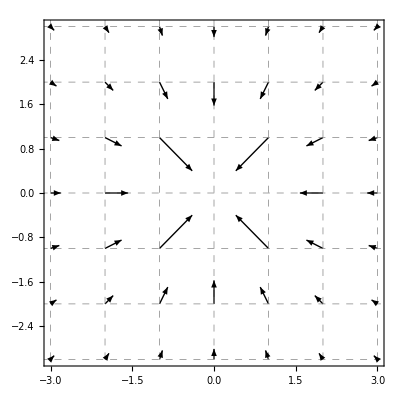

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>1]{-x/(x^2+y^2)^(3/2),-y/(x^2+y^2)^(3/2)},{x,-3,3},{y,-3,3},
PlotRange->{{-3,3},{-3,3}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.5},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/radField4.png",vecField]
```

~/teaching/mooculus/calculus3/vectorFields/radField4.png

```mathematica
Integrate[-y/(x^2+y^2),x]
Integrate[x/(x^2+y^2),y]
```

-ArcTan[x/y]

ArcTan[y/x]

```mathematica
Simplify[(2 x^2)/((x^2+y^2)^2)+(2 y^2)/((x^2+y^2)^2)-2/(x^2+y^2)]
```

0

```mathematica
surface=Plot3D[ArcTan[y,x],{x,-1,1},{y,-1,1},PlotStyle->Opacity[.5],Mesh->False,PlotRange->{-6,6}]
```

-Graphics3D-